## Подготовка набора

```mathematica
SetDirectory@NotebookDirectory[];
{DataColumns=#⟦1⟧,Data=#⟦2;;10001⟧}&@Import["kc_house_data.csv"];
Dimensions[#]&/@%
```

{{21},{10000,21}}

```mathematica
DataColumns
Data⟦1⟧
```

{id,date,price,bedrooms,bathrooms,sqft_living,sqft_lot,floors,waterfront,view,condition,grade,sqft_above,sqft_basement,yr_built,yr_renovated,zipcode,lat,long,sqft_living15,sqft_lot15}

{7129300520,20141013T000000,221900,3,1,1180,5650,1,0,0,3,7,1180,0,1955,0,98178,47.5112,-122.257,1340,5650}

```mathematica
Complement[Range[21],Flatten[Position[DataColumns,#]&/@{"id", "date"}]];
tmpColumns =DataColumns⟦%⟧
Dimensions[tmpData=Data⟦All,%%⟧]
```

{price,bedrooms,bathrooms,sqft_living,sqft_lot,floors,waterfront,view,condition,grade,sqft_above,sqft_basement,yr_built,yr_renovated,zipcode,lat,long,sqft_living15,sqft_lot15}

{10000,19}

```mathematica
Manipulate[Histogram[tmpData⟦All,n⟧,ChartLegends->tmpColumns⟦n⟧,ChartStyle->{{Opacity[.3,Green]}},Frame->True,GridLines->Automatic],{{n,1,"Feature"},1,19,1,SetterBar}]
```

```mathematica
CorrMatrix=Correlation[tmpData];
```

```mathematica
FeatureMap=Partition[Flatten[Table[ListPlot[tmpData⟦;;5000,{i,j}⟧,PlotStyle->{PointSize@Small},FrameTicks->None,Frame->True,FrameLabel->tmpColumns⟦{i,j}⟧,Axes->False,PlotLabel -> Row[{"ρ : ",CorrMatrix⟦i,j⟧}]],{i,3,19},{j,1,1}]],UpTo[3]];
```

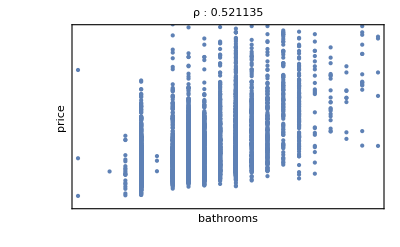
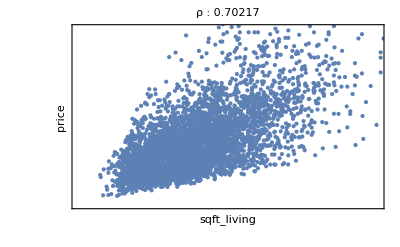
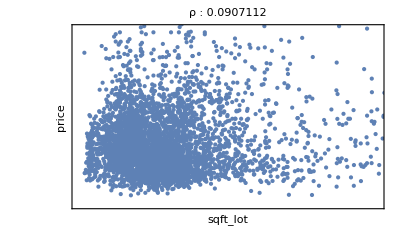
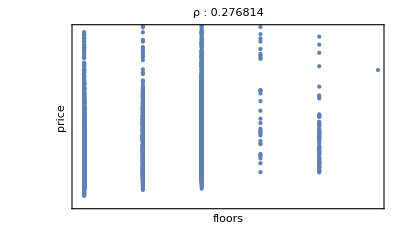
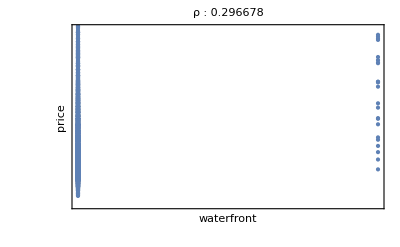
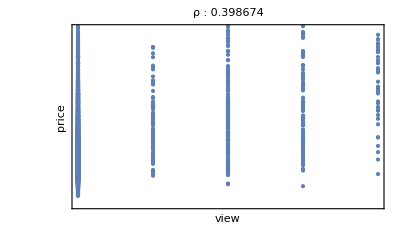
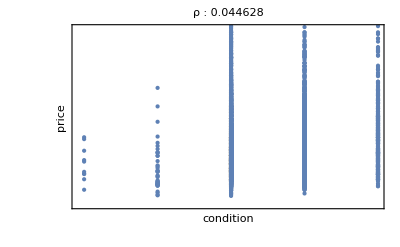
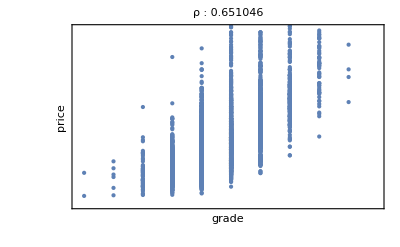
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Grid[FeatureMap]
```

## Выбор необходимых признаков. Стандартизация

```mathematica
Columns={"bathrooms","sqft_living","grade","sqft_above","view","price"};
essentialIndex=Flatten[Position[DataColumns,#]&/@Columns];
n=Length@essentialIndex
```

6

```mathematica
DataMin=Map[Min@#&,Transpose@Data⟦All,essentialIndex⟧];
DataMax=Map[Max@#&,Transpose@Data⟦All,essentialIndex⟧];
Dimensions[DataStd=Map[N@(#-DataMin)/(DataMax-DataMin)&,Data⟦All,essentialIndex⟧]]
{Samples,Target}={DataStd⟦All,;;n-1⟧,DataStd⟦All,n⟧};
Dimensions[#]&/@%
```

{10000,6}

{{10000,5},{10000}}

```mathematica
ClearAll[Train,Test];
{Train,Test}=Partition[RandomSample[Range@10000],UpTo[IntegerPart[0.8*10000]]];
```

```mathematica
Fig0=ListPlot[DataStd⟦Train,{#1,#2}⟧,Frame->True,FrameLabel->{Columns⟦#1⟧,Columns⟦#2⟧}]&;
```

```mathematica
colors=Flatten[Table[{i,j}->ColorData["TemperatureMap",#⟦i,j⟧],{i,1,n-1},{j,1,n-1}]&@Correlation[Samples⟦Train⟧],1];
```

```mathematica
Grid[Floor[Correlation[Samples⟦Train⟧],0.001],ItemSize->{5,5},Background->{None,None,colors},Alignment->Center,Frame->All]
```

0.999 | 0.767 | 0.66 | 0.69 | 0.201
0.767 | 1. | 0.758 | 0.87 | 0.283
0.66 | 0.758 | 0.999 | 0.756 | 0.248
0.69 | 0.87 | 0.756 | 0.999 | 0.163
0.201 | 0.283 | 0.248 | 0.163 | 1.

## Построение линейной модели

```mathematica
Dimensions[Features=Transpose@Prepend[Transpose[Samples⟦Train,{1,5}⟧],ConstantArray[1,Length@Samples⟦Train,{1,5}⟧]]]
```

{8000,3}

```mathematica
ClearAll[W];
W=LeastSquares[Features,Target⟦Train⟧]
```

{-0.00536871,0.235654,0.0754473}

```mathematica
ClearAll[kmPrediction];
kmPrediction[X_]:=W.Prepend[X,1]
```

## Средняя относительная ошибка аппроксимации

```mathematica
average=Mean[Target⟦Test⟧];
predicted=Map[kmPrediction,Samples⟦Test,{1,5}⟧];
```

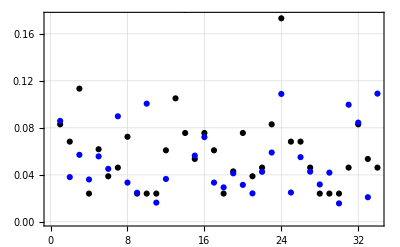

```mathematica
ListPlot[{predicted⟦;;100;;3⟧,Target⟦Test⟦;;100;;3⟧⟧},Frame->True,GridLines->Automatic,PlotStyle->{Black,Blue}]
```

```mathematica
Plus@@Abs[(predicted-Target⟦Test⟧)/predicted];
%/Length@Test
```

0.451845